Partes de listas

Part elige un elemento de una lista.

Elija el elemento 2 de una lista:

```mathematica
Part[{a,b,c,d,e,f,g},2]
```

b

[[ ... ]] es una notación alternativa.

Use [[2]] para elegir el elemento número 2 de una lista:

```mathematica
{a,b,c,d,e,f,g}[[2]]
```

b

Los números de parte negativos cuentan a partir del final de una lista:

```mathematica
{a,b,c,d,e,f,g}[[-2]]
```

f

Puede pedirse una lista de partes mediante la lista de los números de parte.

Elija las partes 2, 4 y 5:

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]]
```

{b,d,e}

;; sirve para obtener un tramo o secuencia de partes.

Elija las partes, de la 2 a la 5:

```mathematica
{a,b,c,d,e,f,g}[[2;;5]]
```

{b,c,d,e}

Tome los 4 primeros elementos de una lista:

```mathematica
Take[{a,b,c,d,e,f,g},4]
```

{a,b,c,d}

Tome los 2 últimos elementos de una lista:

```mathematica
Take[{a,b,c,d,e,f,g},-2]
```

{f,g}

La lista sin sus 2 últimos elementos:

```mathematica
Drop[{a,b,c,d,e,f,g},-2]
```

{a,b,c,d,e}

Ahora se consideran listas de listas, o arreglos. Cada sublista juega el papel de una fila en el arreglo.

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}//Grid
```

a | b | c
d | e | f
g | h | i

Elija la segunda sublista, que corresponde a la segunda fila del arreglo:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2]]
```

{d,e,f}

Aquí se va a elegir el elemento 1 de la fila 2:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,1]]
```

d

También se pueden elegir columnas de un arreglo.

Ahora se elige la primera columna, tomando el elemento 1 de cada fila:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,1]]
```

{a,d,g}

La función Position obtiene la lista de las posiciones donde se ubica alguna cosa.

En lo que sigue hay solamente una d, que aparece en la posición 2,1:

```mathematica
Position[{{a,b,c},{d,e,f},{g,h,i}},d]
```

{{2,1}}

Aquí se obtiene la lista de todas las posiciones donde aparece x:

```mathematica
Position[{{x,y,x},{y,y,x},{x,y,y},{x,x,y}},x]
```

{{1,1},{1,3},{2,3},{3,1},{4,1},{4,2}}

En una lista de caracteres, las posiciones donde aparece la “a”:

```mathematica
Position[Characters["The Wolfram Language"],"a"]
```

{{10},{14},{18}}

En la secuencia de dígitos de 2^500, encontrar las posiciones donde aparece 0 :

```mathematica
Flatten[Position[IntegerDigits[2^500],0]]
```

{7,9,19,20,44,47,50,65,75,88,89,96,103,115,116,119,120,137}

La función ReplacePart efectúa la sustitución de partes de una lista:

Sustituya la parte 3 con x:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},3->x]
```

{a,b,x,d,e,f,g}

Sustituya en dos partes:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{3->x,5->y}]
```

{a,b,x,d,y,f,g}

Sustituya 5 partes con “--” , elegidas al azar:

```mathematica
ReplacePart[Characters["The Wolfram Language"],Table[RandomInteger[{1,20}]->"--",5]]
```

{T,h,e, ,W,--,l,f,r,a,m,--,--,--,n,g,u,a,g,--}

A veces se desea que desaparezcan de una lista ciertas partes dadas. Esto puede hacerse sustituyéndolas con Nothing.

Nothing sencillamente borra:

```mathematica
{1,2,Nothing,4,5,Nothing}
```

{1,2,4,5}

Sustituya las partes 1 y 3 con Nothing:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{1->Nothing,3->Nothing}]
```

{b,d,e,f,g}

Tome 50 palabras del inglés al azar, eliminando aquellas que tengan más de 5 caracteres e invierta el orden de las que queden:

```mathematica
If[StringLength[#]>5,Nothing,StringReverse[#]]&/@RandomSample[WordList[ ],50]
```

{yllud,yciuj,poons,tsioh}

Take elige un número especificado de los elementos de una lista con base en sus posiciones. TakeLargest y TakeSmallest elige los elementos con base en sus tamaños.

Obtener los 5 elementos más grandes de una lista:

```mathematica
TakeLargest[Range[20],5]
```

{20,19,18,17,16}

TakeLargestBy y TakeSmallestBy elige los elementos de acuerdo con la aplicación de alguna función.

Proporcione los 100 primeros números romanos, tome los 5 que tengan las mayores longitudes de cadena de sus caracteres:

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

{LXXXVIII,LXXXIII,XXXVIII,LXXVIII,LXXXVII}

Vocabulario

Part[lista,n] |   | parte n de una lista
lista[[n]] |   | notación abreviada para la parte n de una lista
lista[[{n_1,n_2,...}]] |   | lista de las partes n_1, n_2, ...
lista[[n_1;;n_2]] |   | extensión (secuencia) de las partes n_1 hasta n_2
lista[[m,n]] |   | elemento en la fila m, columna n de un arreglo
lista[[All,n]] |   | todos los elementos de la columna n
Take[lista,n] |   | toma los n primeros elementos de una lista
TakeLargest[lista,n] |   | toma los n elementos más grandes de una lista
TakeSmallest[lista,n] |   | toma los n elementos más pequeños de una lista
TakeLargestBy[lista,f,n] |   | toma los elementos más grandes al aplicar f
TakeSmallestBy[lista,f,n] |   | toma los elementos más pequeños al aplicar f
Position[lista,x] |   | todas las posiciones en que se encuentra x en lista
ReplacePart[lista,n→x] |   | sustituye con x la parte n de lista
Nothing |   | elemento que se elimina automáticamente en una lista

"13 Exercises Available" | "Get Started »"

Encuentre los 5 últimos dígitos de 2^1000. »

| Expected output: |  
  | {6,9,3,7,6} |

Obtenga las letras de la 10 a la 20 del alfabeto inglés. »

| Expected output: |  
  | {"j","k","l","m","n","o","p","q","r","s","t"} |

Forme la lista de las letras en las posiciones pares del alfabeto inglés. »

| Expected output: |  
  | {"b","d","f","h","j","l","n","p","r","t","v","x","z"} |

Obtenga el gráfico con los puntos unidos del penúltimo dígito en las 100 primeras potencias de 12. »

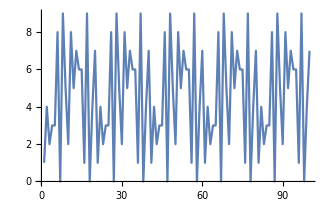
| Expected output: |  
  | -Graphics- |

Junte las listas de los 20 primeros cuadrados y cubos, y obtenga los 10 elementos más pequeños de la lista combinada. »

| Expected output: |  
  | {1,1,4,8,9,16,25,27,36,49} |

Encuentre las posiciones de la palabra “software” en el artículo “computers” en Wikipedia. »

| Sample expected output: |  
  | {4594,4732,4739,4747,4769,6070,6164,6186,7608,7665,7687} |

Produzca el histograma de las posiciones donde aparece la letra “e” en las palabras de WordList[ ]. »

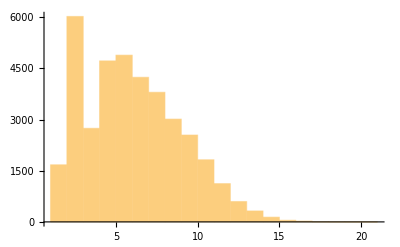
| Expected output: |  
  | -Graphics- |

Construya la lista de los 100 primeros cubos, sustituyendo con rojo (Red en inglés) aquellos cuya posición sea un cuadrado. »

| Expected output: |  
  | {RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]} |

Forme la lista de los 100 primeros primos, eliminando aquellos cuyo primer dígito sea menor que 5. »

| Expected output: |  
  | {5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541} |

Construya una rejilla, comenzando con Range[10] y, entonces, en cada uno de 9 pasos seguidos, eliminar un elemento al azar. »

| Sample expected output: |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 3 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
3 | 5 | 6 | 7 | 8 | 9 | 10 |  |  | 
3 | 6 | 7 | 8 | 9 | 10 |  |  |  | 
3 | 6 | 7 | 9 | 10 |  |  |  |  | 
3 | 6 | 7 | 9 |  |  |  |  |  | 
6 | 7 | 9 |  |  |  |  |  |  | 
7 | 9 |  |  |  |  |  |  |  | 
9 |  |  |  |  |  |  |  |  |  |

Encuentre las 10 palabras más largas en WordList[ ]. »

| Expected output: |  
  | {"electroencephalographic","electroencephalograph","counterrevolutionary","buckminsterfullerene","compartmentalization","electroencephalogram","internationalization","uncharacteristically","magnetohydrodynamics","incomprehensibility"} |

Encuentre los nombres en inglés más largos de los números enteros del 1 al 100. »

| Expected output: |  
  | {"seventy-seven","seventy-three","seventy-eight","twenty-three","twenty-eight"} |

Encuentre los 5 nombres en inglés de los enteros hasta el 100, que contengan en ellos la mayor cantidad de “e”s. »

| Expected output: |  
  | {"seventy-three","seventeen","seventy-seven","nineteen","eleven"} |

Preguntas y respuestas

¿Cómo se dice en voz alta lista[[n]]?

Generalmente, como “lista parte n” o “lista sub n”. La segunda forma (donde “sub” es la abreviatura de “subíndice”) proviene de cómo se hace referencia a los componentes de vectores en matemáticas.

¿Qué sucede si se pide una parte que no exista en una lista?

Se recibe un mensaje, y la entrada original se regresa tal cual.

¿Puede obtenerse solamente la primera posición donde aparece alguna cosa en una lista?

Sí. Use FirstPosition.

Notas técnicas

First y Last equivalen a [[1]] y [[-1]].

Al especificar partes, 1;;-1 equivale a All.

Para explorar más

Guía para partes de listas en Wolfram Language »